```mathematica
(* initial_segmentation_spheroid allows a very crude segmentation of cells in a stack of images via a merger of nearest neighbours *)
```

## Auxiliary code

### plot2DSegment

```mathematica
ClearAll[plot2DSegmentationViewer,cellData,plotcentroid,plotIDs];
plot2DSegmentationViewer[stack_,centroids_,dH_]:= Module[{cellcentroids},
cellcentroids = Round@centroids[[All,2]];
cellData = cellcentroids//Abs@({0,0,dH}-#)&/@#&//Map[RotateLeft[#,2]&,#]&;
plotcentroid={};plotIDs={};
Manipulate[
Module[{IDpos,infocus,z=i},
IDpos=Position[cellData[[All,1]],i_/;(z-2<i<z+2)];
infocus=Extract[cellData,IDpos];
If[Length@infocus>0,
plotcentroid=ListPlot[infocus[[All,{2,3}]],PlotStyle-> {Blue,PointSize[0.01]}];
plotIDs = Graphics[{White,MapThread[Inset[ToString[#1],#2]&,{Flatten[IDpos],infocus[[All,{2,3}]]}]}];
]
];
Show[Colorize@stack[[i]],plotcentroid,plotIDs]
,{i,3,dH-2,1}]
];
```

## Initial Segmentation

```mathematica
(* numerical values used: 20, 100, 0.01 *)
```

```mathematica
Clear@intialSeg;
intialSeg[filename_?StringQ]:=Module[{stack,img3D,imgData,imgDim,roi,img3DBin,imgBinData,imgDataDim,height, fillholes,distance,markers, seg, areas,
background,centroids},

stack =  Import@filename;
img3D = Image3D[stack];
imgDim = ImageDimensions@img3D;
roi = {ConstantArray[1,3],Reverse@imgDim}ᵀ;
img3D = ImageTake[img3D,##]&@@roi;

img3DBin =Binarize[img3D];
imgBinData = ImageData[img3DBin]; (* data from binarized 3d image *)
imgData = ImageData[img3D]; (* data from non-binarized 3d image *)
imgDataDim =Dimensions[imgData];
height = First@imgDataDim;
(* now let us fill small-holes and gaps *)
fillholes[imagedata_,size_]:= Block[{img = imagedata, filledImage},
filledImage = (FillingTransform@Image[img])~DeleteSmallComponents~size;
ImageData[filledImage]
];
 Do[
imgData[[i]] = imgData[[i]]~fillholes ~20;
imgBinData[[i]] = imgBinData[[i]]~fillholes~20;
,{i,height}
]; 
img3D = Image3D[imgData]//DeleteSmallComponents[#,100]&;
img3DBin = Image3D[imgBinData]//DeleteSmallComponents[#,100]&;

(* after filling holes we need to find seeds and segment the image using watershed *)
distance = ImageAdjust@DistanceTransform[img3DBin,Padding-> 0] ;(* distance transform of the image *)
markers = MaxDetect[distance,0.01]; (* markers for segmentation *)
seg = WatershedComponents[GradientFilter[img3D,2],markers,Method->"Rainfall"]; (* watershed on non-binarized 3D image *)
(* removing background *)
areas = ComponentMeasurements[seg,"Area"]; 
background = MaximalBy[areas,Last][[1,1]];  
seg = ArrayComponents[seg,Length@areas,background-> 0];
centroids = ComponentMeasurements[seg,"Centroid"];
Print@Colorize[seg];
seg
];
```

```mathematica
file = "C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C0.tif";
seg=intialSeg[file];
```

## merge tiny blobs with their bigger neighbours

```mathematica
Clear@mergeNeighbours;
mergeNeighbours[seg_?ArrayQ]:=Module[{areasM, ncM,centroidsM,areaval,neighboursM,assoc,mergecandidates,closecentroids,nearest,nearestpairList,nearestneighboursList,mergeNeighboursHelper,
maxdistance,offset,position,segT=seg},

offset=10000;maxdistance=7.0;areaval=15000;
{areasM,ncM,centroidsM,neighboursM} =Map[ComponentMeasurements[seg,#]&,{"Area","NeighborCount","Centroid","Neighbors"}];

mergeNeighboursHelper[lis_,pat:{_,_}]:= Module[{indices},
indices=#1&@@@Position[nearestpairList,pat[[#]]]&/@{1,2};
If[Length@indices>1,
Join[lis,{Union@Flatten@Extract[nearestpairList,Partition[indices,1]]}],
Join[lis,{pat}]]
];
assoc=Merge[{Association@areasM,Association@ncM},List@@#&]; 
mergecandidates = Keys@Select[assoc,(#[[1]]<areaval&&#[[2]]>0&)];(* cells with at least one neighbour and a size smaller than some value *)
(* the part below finds the nearestneighbours of the individual cells in mergecandidates and sows the closest neighbour with the cell. any duplicate entries such as {cell1,cell2} and {cell2,cell1} are deleted. *)
nearestpairList=
Reap@If[mergecandidates≠ {},
Table[closecentroids=Reverse/@Extract[centroidsM,Partition[neighboursM[[i]][[2]],1]];
nearest=Nearest[closecentroids,Last@@centroidsM[[i]],{1,maxdistance}];
If[nearest≠{},Sow[{i,First@nearest}]],{i,mergecandidates}];
];
(* if one cell is also the nearest neighbour of another cell-pair then merge all the cells together *)
If[Last@nearestpairList≠ {},
(nearestpairList=DeleteDuplicates@*Map[Sort]@*First@*Last@nearestpairList;
nearestneighboursList= SortBy[First]@*Union@Fold[mergeNeighboursHelper,{},nearestpairList]; 
(* here we will reindex: merge the neighbouring cells together *)
Do[position=Position[segT,Alternatives@@i];
segT=ReplacePart[segT,Thread[position-> offset]];
offset=offset+1,{i,nearestneighboursList}])
];
(* now indexing them back *)
ArrayComponents[segT]
]
```

```mathematica
segM=Nest[mergeNeighbours,seg,3];
```

```mathematica
Colorize@segM
```

-Graphics3D-

```mathematica
primaryStats[seg_]:= Module[{areasM,ncM,centroidsM,neighboursM,avgcellsize,areaval},
{areasM,ncM,centroidsM,neighboursM} =Map[ComponentMeasurements[seg,#]&,{"Area","NeighborCount","Centroid","Neighbors"}];
areaval = areasM[[All,2]];
Print["number of cells: ", Length@areasM];
Print[Style["average cell area in pixels: ",{Bold,Red,FontSize-> 14}],Style[avgcellsize= Mean@areaval,{Bold,FontSize->15}]];
Print@SmoothHistogram[areaval/avgcellsize,PlotStyle->{Thick,XYZColor[0,0,1,0.8]}];
Print@ListPlot[areaval/avgcellsize,PlotStyle->{XYZColor[0,0,1,0.6],PointSize[Large]}];
]
```

number of cells: 412

average cell area in pixels: 16462.4

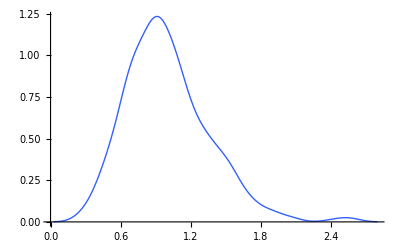

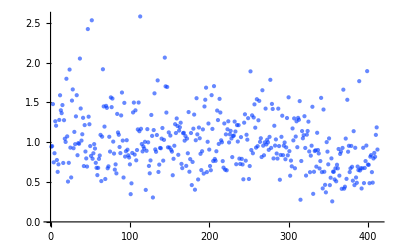

```mathematica
primaryStats[segM]
```

## save initial segmentation

```mathematica
Save[StringReplace[file,".tif"-> ".res"],segM]
```

## 2D segmentation viewer

```mathematica
Get@"C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C0.res";
```

```mathematica
plot2DSegmentationViewer[segM,ComponentMeasurements[segM,"Centroid"],First@Dimensions@segM]
```